## streakline.chpl vs streakline.c

## P5.chpl vs P5.c

## NFWboxpot.chpl vs testRing.chpl

### version 1

#### NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) leapfrog with dimensionless units 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp1pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",1;;10,6;;7}];
bp1pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",10;;20,6;;7}];
bp1pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",100;;110,6;;7}];
bp1pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",200;;210,6;;7}];
bp1pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",300;;310,6;;7}];
bp1pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",990;;1000,6;;7}];
bp1pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",1990;;2000,6;;7}];
bp1pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",2990;;3000,6;;7}];
bp1pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",3990;;4000,6;;7}];
bp1pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",4990;;5000,6;;7}];
bp1pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",5990;;6000,6;;7}];
bp1pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",6990;;7000,6;;7}];
bp1pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",7990;;8000,6;;7}];
bp1pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",8990;;9000,6;;7}];
bp1pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",9990;;10000,6;;7}];

r1pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",1;;10,6;;7}];
r1pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",11;;20,6;;7}];
r1pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",101;;110,6;;7}];
r1pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",201;;210,6;;7}];
r1pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",301;;310,6;;7}];
r1pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",991;;1000,6;;7}];
r1pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",1991;;2000,6;;7}];
r1pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",2991;;3000,6;;7}];
r1pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",3991;;4000,6;;7}];
r1pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",4991;;5000,6;;7}];
r1pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",5991;;6000,6;;7}];
r1pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",6991;;7000,6;;7}];
r1pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",7991;;8000,6;;7}];
r1pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",8991;;9000,6;;7}];
r1pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",9991;;10000,6;;7}];

bp1vel1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",1;;10,9;;10}];
bp1vel2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",10;;20,9;;10}];
bp1vel10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",100;;110,9;;10}];
bp1vel20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",200;;210,9;;10}];
bp1vel30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",300;;310,9;;10}];
bp1vel100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",990;;1000,9;;10}];
bp1vel200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",1990;;2000,9;;10}];
bp1vel300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",2990;;3000,9;;10}];
bp1vel400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",3990;;4000,9;;10}];
bp1vel500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",4990;;5000,9;;10}];
bp1vel600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",5990;;6000,9;;10}];
bp1vel700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",6990;;7000,9;;10}];
bp1vel800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",7990;;8000,9;;10}];
bp1vel900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",8990;;9000,9;;10}];
bp1vel1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp1.csv",{"Data",9990;;10000,9;;10}];
bp1velp1 = {bp1vel1[[1]],bp1vel100[[1]],bp1vel200[[1]],bp1vel300[[1]],bp1vel400[[1]],bp1vel500[[1]],bp1vel600[[1]],bp1vel700[[1]],bp1vel800[[1]],bp1vel900[[1]],bp1vel1000[[1]]}
bp1velp10 = {bp1vel1[[10]],bp1vel100[[10]],bp1vel200[[10]],bp1vel300[[10]],bp1vel400[[10]],bp1vel500[[10]],bp1vel600[[10]],bp1vel700[[10]],bp1vel800[[10]],bp1vel900[[10]],bp1vel1000[[10]]}

r1vel1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",1;;10,9;;10}];
r1vel2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",10;;20,9;;10}];
r1vel10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",100;;110,9;;10}];
r1vel20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",200;;210,9;;10}];
r1vel30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",300;;310,9;;10}];
r1vel100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",990;;1000,9;;10}];
r1vel200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",1990;;2000,9;;10}];
r1vel300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",2990;;3000,9;;10}];
r1vel400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",3990;;4000,9;;10}];
r1vel500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",4990;;5000,9;;10}];
r1vel600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",5990;;6000,9;;10}];
r1vel700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",6990;;7000,9;;10}];
r1vel800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",7990;;8000,9;;10}];
r1vel900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",8990;;9000,9;;10}];
r1vel1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test1.csv",{"Data",9990;;10000,9;;10}];
r1velp1 = {r1vel1[[1]],r1vel100[[1]],r1vel200[[1]],r1vel300[[1]],r1vel400[[1]],r1vel500[[1]],r1vel600[[1]],r1vel700[[1]],r1vel800[[1]],r1vel900[[1]],r1vel1000[[1]]}
r1velp10 = {r1vel1[[10]],r1vel100[[10]],r1vel200[[10]],r1vel300[[10]],r1vel400[[10]],r1vel500[[10]],r1vel600[[10]],r1vel700[[10]],r1vel800[[10]],r1vel900[[10]],r1vel1000[[10]]}
```

{{},{},{},{},{},{},{},{},{},{},{}}

Part::partw: Part 10 of {{}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{{}}⟦10⟧,{{}}⟦10⟧,{{}}⟦10⟧,{{}}⟦10⟧,{{}}⟦10⟧,{{}}⟦10⟧,{{}}⟦10⟧,{{}}⟦10⟧,{{}}⟦10⟧,{{}}⟦10⟧,{{}}⟦10⟧}

{{3.69316,-5.0832},{-5.30544,-3.36614},{-5.64292,2.76321},{-0.594166,6.25506},{5.02181,3.77636},{5.84435,-2.30693},{1.08841,-6.18816},{-4.70646,-4.16272},{-6.00898,1.83615},{-1.57583,6.08235},{4.36141,4.52285}}

{{-1.1542×10^-15,-6.28319},{-6.2664,0.459183},{-2.88421,5.58204},{3.25099,5.37679},{6.28314,0.0392646},{3.31791,-5.33572},{-2.81425,-5.61765},{-6.26021,-0.537457},{-3.73069,5.05581},{2.3598,5.82319},{6.19778,1.03228}}

```mathematica
r1AMp1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM1.csv",{"Data",1;;1000,1}];
r1AMp2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM1.csv",{"Data",1;;1000,2}];
r1AMp3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM1.csv",{"Data",1;;1000,3}];
r1AMp4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM1.csv",{"Data",1;;1000,4}];
r1AMp5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM1.csv",{"Data",1;;1000,5}];
r1AMp6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM1.csv",{"Data",1;;1000,6}];
r1AMp7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM1.csv",{"Data",1;;1000,7}];
r1AMp8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM1.csv",{"Data",1;;1000,8}];
r1AMp9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM1.csv",{"Data",1;;1000,9}];
r1AMp10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM1.csv",{"Data",1;;1000,10}];

bp1AMp1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM1.csv",{"Data",1;;1000,1}];
bp1AMp2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM1.csv",{"Data",1;;1000,2}];
bp1AMp3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM1.csv",{"Data",1;;1000,3}];
bp1AMp4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM1.csv",{"Data",1;;1000,4}];
bp1AMp5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM1.csv",{"Data",1;;1000,5}];
bp1AMp6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM1.csv",{"Data",1;;1000,6}];
bp1AMp7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM1.csv",{"Data",1;;1000,7}];
bp1AMp8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM1.csv",{"Data",1;;1000,8}];
bp1AMp9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM1.csv",{"Data",1;;1000,9}];
bp1AMp10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM1.csv",{"Data",1;;1000,10}];


r1SD = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/SD1.csv",{"Data",1;;1000,1;;2}];
bp1SD = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpSD1.csv",{"Data",1;;1000,1;;2}];

r1PS1 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS1.csv",{"Data",1,1;;4}];
r1PS100 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS1.csv",{"Data",100,1;;4}];
r1PS200 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS1.csv",{"Data",200,1;;4}];
r1PS300 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS1.csv",{"Data",300,1;;4}];
r1PS400 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS1.csv",{"Data",400,1;;4}];
r1PS500 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS1.csv",{"Data",500,1;;4}];
r1PS600 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS1.csv",{"Data",600,1;;4}];
r1PS700 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS1.csv",{"Data",700,1;;4}];
r1PS800 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS1.csv",{"Data",800,1;;4}];
r1PS900 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS1.csv",{"Data",900,1;;4}];
r1PS1000 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS1.csv",{"Data",1000,1;;4}];

bp1PS1 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",1,1;;4}];
bp1PS100 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",100,1;;4}];
bp1PS200 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",200,1;;4}];
bp1PS300 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",300,1;;4}];
bp1PS400 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",400,1;;4}];
bp1PS500 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",500,1;;4}];
bp1PS600 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",600,1;;4}];
bp1PS700 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",700,1;;4}];
bp1PS800 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",800,1;;4}];
bp1PS900 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",900,1;;4}];
bp1PS1000 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",1000,1;;4}];

r1FT1 = Abs[Fourier[{r1PS1}]]^2;
r1FT100 = Abs[Fourier[{r1PS100}]]^2;
r1FT200 = Abs[Fourier[{r1PS200}]]^2;
r1FT300 = Abs[Fourier[{r1PS300}]]^2;
r1FT400 = Abs[Fourier[{r1PS400}]]^2;
r1FT500 = Abs[Fourier[{r1PS500}]]^2;
r1FT600 = Abs[Fourier[{r1PS600}]]^2;
r1FT700 = Abs[Fourier[{r1PS700}]]^2;
r1FT800 = Abs[Fourier[{r1PS800}]]^2;
r1FT900 = Abs[Fourier[{r1PS900}]]^2;
r1FT1000 = Abs[Fourier[{r1PS1000}]]^2;

bp1FT1 = Abs[Fourier[{bp1PS1}]]^2;
bp1FT100 = Abs[Fourier[{bp1PS100}]]^2;
bp1FT200 = Abs[Fourier[{bp1PS200}]]^2;
bp1FT300 = Abs[Fourier[{bp1PS300}]]^2; 
bp1FT400 = Abs[Fourier[{bp1PS400}]]^2;(*start differing here*)
bp1FT500 = Abs[Fourier[{bp1PS500}]]^2;
bp1FT600 = Abs[Fourier[{bp1PS600}]]^2;
bp1FT700 = Abs[Fourier[{bp1PS700}]]^2;
bp1FT800 = Abs[Fourier[{bp1PS800}]]^2;
bp1FT900 = Abs[Fourier[{bp1PS900}]]^2;
bp1FT1000 = Abs[Fourier[{bp1PS1000}]]^2;
```

Fourier::fftl: Argument {{}} is not a non-empty list or rectangular array of numeric quantities.

#### Position

```mathematica
bp1posgraph = ListPlot[{bp1pos1,bp1pos100,bp1pos300,bp1pos400,bp1pos500,bp1pos600,bp1pos700,bp1pos800,bp1pos900,bp1pos1000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

ListPlot[{{{}},{{}},{{}},{{}},{{}},{{}},{{}},{{}},{{}},{{}}},PlotRange→Automatic,AspectRatio→1,ImageSize→Large,PlotLegends→{initial,after 100 timesteps,after 300 timesteps,after 400 timesteps,after 500 timesteps,after 600 timesteps,after 700 timesteps,after 800 timesteps,after 900 timesteps,after 1000 timesteps},AxesLabel→{kpc,kpc},PlotLabel→Position at each timestep]

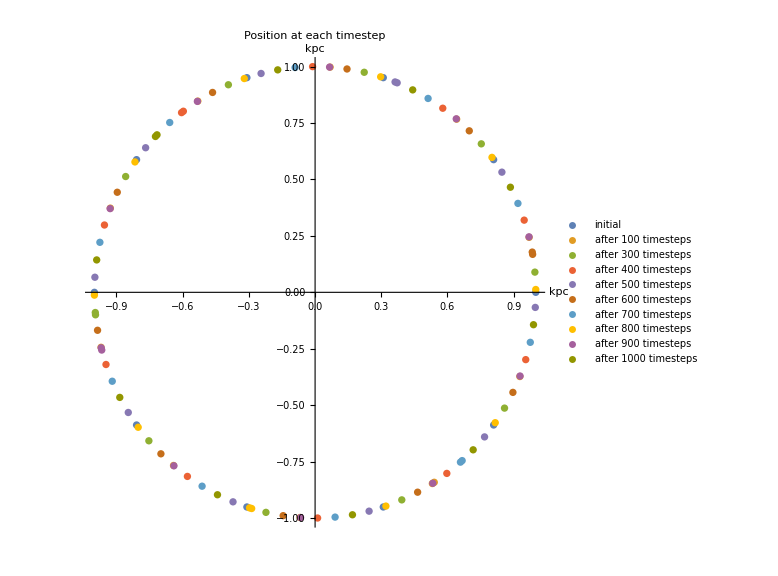

```mathematica
r1posgraph = ListPlot[{r1pos1,r1pos100,r1pos300,r1pos400,r1pos500,r1pos600,r1pos700,r1pos800,r1pos900,r1pos1000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

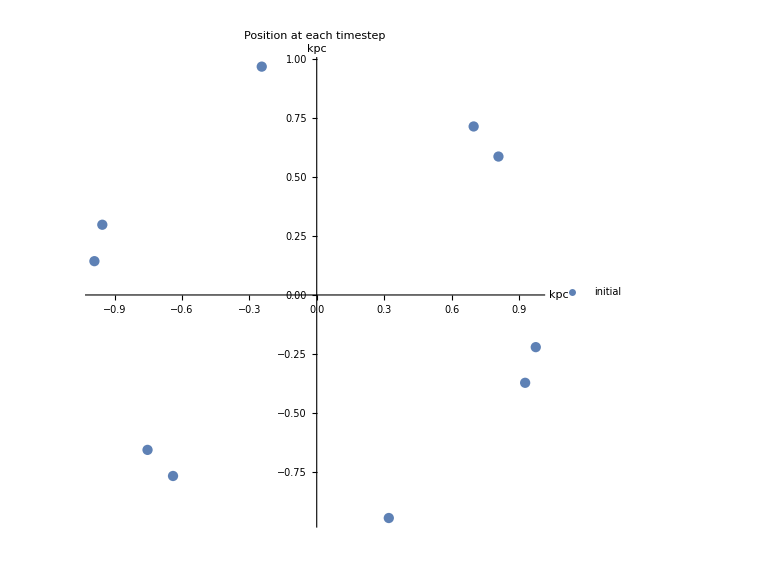

```mathematica
r1pos2graph = ListPlot[{r1pos1[[1]],r1pos100[[1]],r1pos300[[1]],r1pos400[[1]],r1pos500[[1]],r1pos600[[1]],r1pos700[[1]],r1pos800[[1]],r1pos900[[1]],r1pos1000[[1]]},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

```mathematica
comp1graph =  ListPlot[{r1pos1,bp1pos1,r1pos1000,bp1pos1000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"first timestep for testRing","first timestep for bp","last timstep of testRing","last timestep of bp"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

ListPlot::lpn: {{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,1.22465×10^-16},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,-2.44929×10^-16}},{},{{-0.72339,0.690465},{-0.989667,0.143508},{-0.885009,-0.465611},{-0.442308,-0.896882},{0.169339,-0.985576},{0.716305,-0.697812},{0.989667,-0.143508},{0.885009,0.465611},{0.442308,0.896882},{-0.169339,0.985576},«1»},{}} is not a list of numbers or pairs of numbers.

ListPlot[{{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,1.22465×10^-16},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,-2.44929×10^-16}},{{}},{{-0.72339,0.690465},{-0.989667,0.143508},{-0.885009,-0.465611},{-0.442308,-0.896882},{0.169339,-0.985576},{0.716305,-0.697812},{0.989667,-0.143508},{0.885009,0.465611},{0.442308,0.896882},{-0.169339,0.985576},{-0.716305,0.697812}},{{}}},PlotRange→Automatic,AspectRatio→1,ImageSize→Large,PlotLegends→{first timestep for testRing,first timestep for bp,last timstep of testRing,last timestep of bp},AxesLabel→{kpc,kpc},PlotLabel→Position at each timestep]

#### Velocities

```mathematica
vel1graph =  ListPlot[{r1velp1,bp1velp1},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"velocities of first particle of testRing","velocities of first particle of bp","velocities of last particle of testRing","velocities of last particle of bp"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

ListPlot::lpn: {{{3.69316,-5.0832},{-5.30544,-3.36614},{-5.64292,2.76321},{-0.594166,6.25506},{5.02181,3.77636},{5.84435,-2.30693},{1.08841,-6.18816},{-4.70646,-4.16272},{-6.00898,1.83615},{-1.57583,6.08235},«1»},{}} is not a list of numbers or pairs of numbers.

ListPlot[{{{3.69316,-5.0832},{-5.30544,-3.36614},{-5.64292,2.76321},{-0.594166,6.25506},{5.02181,3.77636},{5.84435,-2.30693},{1.08841,-6.18816},{-4.70646,-4.16272},{-6.00898,1.83615},{-1.57583,6.08235},{4.36141,4.52285}},{{},{},{},{},{},{},{},{},{},{},{}}},PlotRange→Automatic,AspectRatio→1,ImageSize→Large,PlotLegends→{velocities of first particle of testRing,velocities of first particle of bp,velocities of last particle of testRing,velocities of last particle of bp},AxesLabel→{kpc,kpc},PlotLabel→Position at each timestep]

#### Angular Momentum

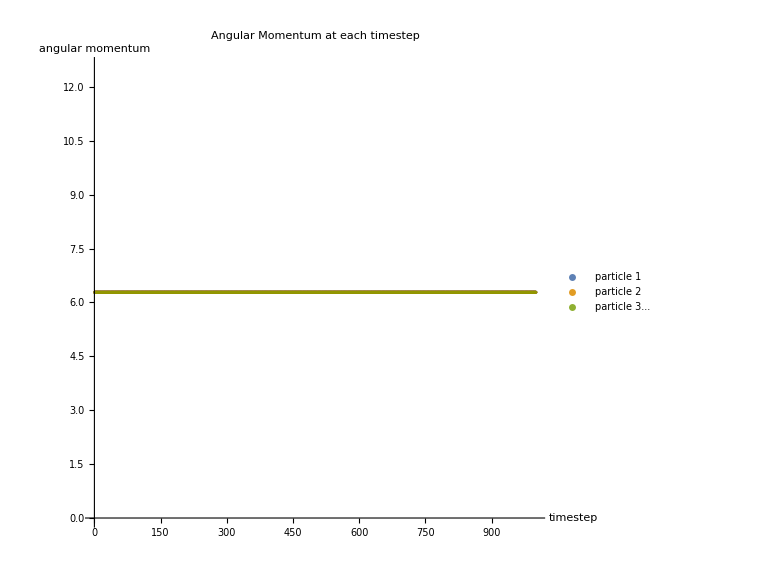

```mathematica
r1AMgraph = ListPlot[{r1AMp1,r1AMp2,r1AMp3,r1AMp4,r1AMp5,r1AMp6,r1AMp7,r1AMp8,r1AMp9,r1AMp10},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"particle 1","particle 2","particle 3..."},AxesLabel->{"timestep","angular momentum"}, PlotLabel-> "Angular Momentum at each timestep"]
```

```mathematica
bp1AMgraph = ListPlot[{r1AMp1,r1AMp2,r1AMp3,r1AMp4,r1AMp5,r1AMp6,r1AMp7,r1AMp8,r1AMp9,r1AMp10},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"particle 1","particle 2","particle 3..."},AxesLabel->{"timestep","angular momentum"}, PlotLabel-> "Angular Momentum at each timestep"]
```

-Graphics-

#### Velocity Dispersion

```mathematica
SD1graph = ListPlot[{r1SD,bp1SD},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"testRing","box potential"},AxesLabel->{"timestep","standard deviation of velocity"}, PlotLabel-> "Velocity Dispersion"]
```

ListPlot::lpn: {{{0.,9.4645×10^-15},{1.,1.15916×10^-14},{2.,1.15916×10^-14},{3.,1.6393×10^-14},{4.,2.59196×10^-14},{5.,2.91715×10^-14},{6.,2.41298×10^-14},{7.,2.75935×10^-14},{8.,2.50407×10^-14},{9.,2.50407×10^-14},«990»},{}} is not a list of numbers or pairs of numbers.

ListPlot[{{{0,9.4645×10^-15},{1,1.15916×10^-14},{2,1.15916×10^-14},{3,1.6393×10^-14},{4,2.59196×10^-14},{5,2.91715×10^-14},{6,2.41298×10^-14},{7,2.75935×10^-14},{8,2.50407×10^-14},{9,2.50407×10^-14},{10,2.75935×10^-14},{11,2.59196×10^-14},{12,2.50407×10^-14},{13,1.8929×10^-14},{14,2.99294×10^-14},{15,3.54129×10^-14},{16,3.06685×10^-14},{17,2.50407×10^-14},{18,2.99294×10^-14},{19,1.8929×10^-14},{20,2.21962×10^-14},{21,2.00772×10^-14},{22,2.50407×10^-14},{23,2.00772×10^-14},{24,2.59196×10^-14},{25,2.50407×10^-14},{26,2.99294×10^-14},{27,3.2786×10^-14},{28,3.06685×10^-14},{29,2.67696×10^-14},{30,3.2786×10^-14},{31,2.83935×10^-14},{32,3.2786×10^-14},{33,3.54129×10^-14},{34,3.54129×10^-14},{35,3.95928×10^-14},{36,2.75935×10^-14},{37,2.83935×10^-14},{38,3.34621×10^-14},{39,3.20957×10^-14},{40,3.06685×10^-14},{41,2.91715×10^-14},{42,2.75935×10^-14},{43,3.20957×10^-14},{44,3.41247×10^-14},{45,4.01545×10^-14},{46,3.7858×10^-14},{47,3.90231×10^-14},{48,3.95928×10^-14},{49,3.20957×10^-14},{50,3.54129×10^-14},{51,3.90231×10^-14},{52,4.17941×10^-14},{53,3.66558×10^-14},{54,3.13902×10^-14},{55,3.13902×10^-14},{56,3.2786×10^-14},{57,3.13902×10^-14},{58,3.47748×10^-14},{59,3.06685×10^-14},{60,3.2786×10^-14},{61,3.72618×10^-14},{62,3.66558×10^-14},{63,2.67696×10^-14},{64,3.13902×10^-14},{65,3.90231×10^-14},{66,2.41298×10^-14},{67,2.99294×10^-14},{68,2.67696×10^-14},{69,2.75935×10^-14},{70,2.99294×10^-14},{71,2.67696×10^-14},{72,3.41247×10^-14},{73,2.75935×10^-14},{74,2.21962×10^-14},{75,2.67696×10^-14},{76,3.13902×10^-14},{77,3.66558×10^-14},{78,2.99294×10^-14},{79,3.20957×10^-14},{80,3.06685×10^-14},{81,3.60397×10^-14},{82,3.54129×10^-14},{83,3.8445×10^-14},{84,3.90231×10^-14},{85,3.90231×10^-14},{86,4.9179×10^-14},{87,3.8445×10^-14},{88,4.01545×10^-14},{89,4.17941×10^-14},{90,3.60397×10^-14},{91,5.5187×10^-14},{92,5.91058×10^-14},{93,5.18392×10^-14},{94,5.47798×10^-14},{95,4.63664×10^-14},{96,5.00814×10^-14},{97,4.48941×10^-14},{98,5.22694×10^-14},{99,5.39559×10^-14},{100,5.59927×10^-14},{101,5.75703×10^-14},{102,6.5572×10^-14},{103,5.05266×10^-14},{104,5.22694×10^-14},{105,4.23265×10^-14},{106,4.23265×10^-14},{107,5.35393×10^-14},{108,4.38851×10^-14},{109,5.35393×10^-14},{110,5.18392×10^-14},{111,5.09679×10^-14},{112,4.43924×10^-14},{113,5.22694×10^-14},{114,4.73225×10^-14},{115,4.07084×10^-14},{116,3.20957×10^-14},{117,4.12548×10^-14},{118,3.72618×10^-14},{119,3.54129×10^-14},{120,3.72618×10^-14},{121,4.28523×10^-14},{122,4.77934×10^-14},{123,4.28523×10^-14},{124,3.72618×10^-14},{125,4.28523×10^-14},{126,4.43924×10^-14},{127,6.02317×10^-14},{128,4.23265×10^-14},{129,4.43924×10^-14},{130,5.00814×10^-14},{131,4.07084×10^-14},{132,3.7858×10^-14},{133,4.01545×10^-14},{134,4.01545×10^-14},{135,4.53901×10^-14},{136,3.90231×10^-14},{137,3.66558×10^-14},{138,3.95928×10^-14},{139,3.66558×10^-14},{140,4.53901×10^-14},{141,3.7858×10^-14},{142,4.43924×10^-14},{143,3.66558×10^-14},{144,4.96323×10^-14},{145,4.12548×10^-14},{146,4.82597×10^-14},{147,4.53901×10^-14},{148,4.68469×10^-14},{149,4.73225×10^-14},{150,4.87215×10^-14},{151,5.18392×10^-14},{152,5.14054×10^-14},{153,5.14054×10^-14},{154,5.14054×10^-14},{155,5.47798×10^-14},{156,5.5187×10^-14},{157,5.35393×10^-14},{158,5.14054×10^-14},{159,5.26961×10^-14},{160,4.9179×10^-14},{161,4.17941×10^-14},{162,4.73225×10^-14},{163,4.63664×10^-14},{164,5.22694×10^-14},{165,5.09679×10^-14},{166,5.09679×10^-14},{167,4.53901×10^-14},{168,4.63664×10^-14},{169,4.73225×10^-14},{170,5.18392×10^-14},{171,4.53901×10^-14},{172,4.73225×10^-14},{173,4.96323×10^-14},{174,4.68469×10^-14},{175,4.33718×10^-14},{176,5.18392×10^-14},{177,4.68469×10^-14},{178,5.31194×10^-14},{179,4.48941×10^-14},{180,4.48941×10^-14},{181,5.6787×10^-14},{182,6.09708×10^-14},{183,5.94835×10^-14},{184,5.91058×10^-14},{185,5.91058×10^-14},{186,6.45393×10^-14},{187,6.41914×10^-14},{188,6.52296×10^-14},{189,5.98588×10^-14},{190,5.718×10^-14},{191,5.5187×10^-14},{192,5.35393×10^-14},{193,6.09708×10^-14},{194,6.27804×10^-14},{195,6.65887×10^-14},{196,5.7958×10^-14},{197,5.26961×10^-14},{198,5.6787×10^-14},{199,5.5187×10^-14},{200,5.6787×10^-14},{201,5.87257×10^-14},{202,6.1701×10^-14},{203,5.75703×10^-14},{204,5.09679×10^-14},{205,5.22694×10^-14},{206,5.39559×10^-14},{207,6.38415×10^-14},{208,6.24227×10^-14},{209,6.24227×10^-14},{210,6.20629×10^-14},{211,5.7958×10^-14},{212,5.35393×10^-14},{213,5.39559×10^-14},{214,4.9179×10^-14},{215,5.26961×10^-14},{216,5.87257×10^-14},{217,5.98588×10^-14},{218,5.22694×10^-14},{219,5.35393×10^-14},{220,4.96323×10^-14},{221,4.96323×10^-14},{222,4.82597×10^-14},{223,5.05266×10^-14},{224,4.73225×10^-14},{225,4.73225×10^-14},{226,3.7858×10^-14},{227,4.73225×10^-14},{228,3.7858×10^-14},{229,3.90231×10^-14},{230,3.72618×10^-14},{231,2.91715×10^-14},{232,3.06685×10^-14},{233,2.99294×10^-14},{234,2.50407×10^-14},{235,3.60397×10^-14},{236,3.60397×10^-14},{237,3.41247×10^-14},{238,3.8445×10^-14},{239,4.01545×10^-14},{240,3.95928×10^-14},{241,3.54129×10^-14},{242,3.95928×10^-14},{243,4.23265×10^-14},{244,3.95928×10^-14},{245,4.23265×10^-14},{246,3.2786×10^-14},{247,4.43924×10^-14},{248,4.9179×10^-14},{249,4.38851×10^-14},{250,4.01545×10^-14},{251,3.7858×10^-14},{252,4.38851×10^-14},{253,3.8445×10^-14},{254,3.8445×10^-14},{255,4.17941×10^-14},{256,4.07084×10^-14},{257,3.54129×10^-14},{258,3.7858×10^-14},{259,4.12548×10^-14},{260,3.41247×10^-14},{261,4.12548×10^-14},{262,3.66558×10^-14},{263,4.53901×10^-14},{264,4.68469×10^-14},{265,5.09679×10^-14},{266,5.18392×10^-14},{267,6.06024×10^-14},{268,6.48853×10^-14},{269,5.75703×10^-14},{270,5.18392×10^-14},{271,4.58809×10^-14},{272,5.7958×10^-14},{273,6.65887×10^-14},{274,6.72579×10^-14},{275,6.89026×10^-14},{276,6.98708×10^-14},{277,8.03089×10^-14},{278,8.00296×10^-14},{279,7.9468×10^-14},{280,7.42224×10^-14},{281,7.80463×10^-14},{282,8.05873×10^-14},{283,7.91857×10^-14},{284,8.5443×10^-14},{285,8.41223×10^-14},{286,8.11412×10^-14},{287,8.5443×10^-14},{288,8.8279×10^-14},{289,8.30506×10^-14},{290,9.20055×10^-14},{291,8.70014×10^-14},{292,7.89024×10^-14},{293,9.07803×10^-14},{294,8.35882×10^-14},{295,8.30506×10^-14},{296,8.11412×10^-14},{297,7.80463×10^-14},{298,8.22377×10^-14},{299,8.87849×10^-14},{300,8.27806×10^-14},{301,7.8618×10^-14},{302,8.27806×10^-14},{303,8.27806×10^-14},{304,8.25096×10^-14},{305,8.41223×10^-14},{306,8.57047×10^-14},{307,8.41223×10^-14},{308,8.67436×10^-14},{309,8.03089×10^-14},{310,7.9468×10^-14},{311,9.00372×10^-14},{312,9.39325×10^-14},{313,9.55868×10^-14},{314,9.32145×10^-14},{315,9.36938×10^-14},{316,9.2974×10^-14},{317,9.27328×10^-14},{318,9.32145×10^-14},{319,8.80249×10^-14},{320,8.85323×10^-14},{321,8.33199×10^-14},{322,8.62257×10^-14},{323,8.38557×10^-14},{324,9.813×10^-14},{325,8.51805×10^-14},{326,8.33199×10^-14},{327,8.62257×10^-14},{328,7.77588×10^-14},{329,8.49172×10^-14},{330,7.91857×10^-14},{331,8.35882×10^-14},{332,7.91857×10^-14},{333,8.33199×10^-14},{334,9.22485×10^-14},{335,8.87849×10^-14},{336,9.05333×10^-14},{337,9.65193×10^-14},{338,8.87849×10^-14},{339,9.44081×10^-14},{340,9.4645×10^-14},{341,8.85323×10^-14},{342,8.35882×10^-14},{343,8.16913×10^-14},{344,9.2491×10^-14},{345,8.43881×10^-14},{346,8.90367×10^-14},{347,8.16913×10^-14},{348,7.97493×10^-14},{349,8.80249×10^-14},{350,8.75146×10^-14},{351,8.80249×10^-14},{352,8.87849×10^-14},{353,9.07803×10^-14},{354,8.62257×10^-14},{355,9.22485×10^-14},{356,8.5443×10^-14},{357,8.67436×10^-14},{358,9.07803×10^-14},{359,8.51805×10^-14},{360,7.9468×10^-14},{361,8.51805×10^-14},{362,8.08647×10^-14},{363,8.25096×10^-14},{364,7.83327×10^-14},{365,7.30056×10^-14},{366,7.14554×10^-14},{367,6.98708×10^-14},{368,5.98588×10^-14},{369,6.20629×10^-14},{370,5.87257×10^-14},{371,5.98588×10^-14},{372,6.59126×10^-14},{373,6.02317×10^-14},{374,5.39559×10^-14},{375,5.31194×10^-14},{376,6.34898×10^-14},{377,6.1701×10^-14},{378,6.79206×10^-14},{379,6.27804×10^-14},{380,6.45393×10^-14},{381,6.1337×10^-14},{382,7.48234×10^-14},{383,6.98708×10^-14},{384,6.79206×10^-14},{385,7.42224×10^-14},{386,6.98708×10^-14},{387,6.34898×10^-14},{388,6.38415×10^-14},{389,6.89026×10^-14},{390,7.54197×10^-14},{391,7.51221×10^-14},{392,7.23895×10^-14},{393,7.08258×10^-14},{394,7.11413×10^-14},{395,7.60112×10^-14},{396,7.77588×10^-14},{397,6.72579×10^-14},{398,7.8618×10^-14},{399,8.05873×10^-14},{400,7.97493×10^-14},{401,6.82495×10^-14},{402,7.65982×10^-14},{403,7.71807×10^-14},{404,7.5716×10^-14},{405,8.00296×10^-14},{406,7.91857×10^-14},{407,8.08647×10^-14},{408,7.39201×10^-14},{409,6.92268×10^-14},{410,7.23895×10^-14},{411,7.71807×10^-14},{412,7.8618×10^-14},{413,7.97493×10^-14},{414,8.35882×10^-14},{415,8.72584×10^-14},{416,8.85323×10^-14},{417,8.41223×10^-14},{418,9.2491×10^-14},{419,9.05333×10^-14},{420,8.85323×10^-14},{421,8.35882×10^-14},{422,9.07803×10^-14},{423,8.14167×10^-14},{424,8.87849×10^-14},{425,8.5443×10^-14},{426,8.33199×10^-14},{427,8.25096×10^-14},{428,8.6485×10^-14},{429,8.75146×10^-14},{430,8.5443×10^-14},{431,8.43881×10^-14},{432,9.00372×10^-14},{433,9.22485×10^-14},{434,8.67436×10^-14},{435,8.85323×10^-14},{436,8.6485×10^-14},{437,8.38557×10^-14},{438,8.35882×10^-14},{439,8.5443×10^-14},{440,7.80463×10^-14},{441,7.89024×10^-14},{442,7.80463×10^-14},{443,7.9468×10^-14},{444,7.54197×10^-14},{445,8.11412×10^-14},{446,8.62257×10^-14},{447,8.51805×10^-14},{448,9.00372×10^-14},{449,9.17617×10^-14},{450,9.00372×10^-14},{451,8.11412×10^-14},{452,8.43881×10^-14},{453,8.59656×10^-14},{454,9.10266×10^-14},{455,8.80249×10^-14},{456,9.79015×10^-14},{457,9.48813×10^-14},{458,9.48813×10^-14},{459,9.79015×10^-14},{460,9.41706×10^-14},{461,9.79015×10^-14},{462,1.02155×10^-13},{463,9.6287×10^-14},{464,1.02155×10^-13},{465,1.00386×10^-13},{466,9.72129×10^-14},{467,9.60542×10^-14},{468,9.67511×10^-14},{469,9.58208×10^-14},{470,9.67511×10^-14},{471,9.27328×10^-14},{472,9.88123×10^-14},{473,9.60542×10^-14},{474,9.7443×10^-14},{475,9.6287×10^-14},{476,9.12723×10^-14},{477,9.44081×10^-14},{478,9.67511×10^-14},{479,8.72584×10^-14},{480,8.30506×10^-14},{481,8.38557×10^-14},{482,9.2974×10^-14},{483,9.00372×10^-14},{484,8.6485×10^-14},{485,8.22377×10^-14},{486,8.22377×10^-14},{487,8.22377×10^-14},{488,8.43881×10^-14},{489,8.25096×10^-14},{490,8.08647×10^-14},{491,8.38557×10^-14},{492,8.30506×10^-14},{493,8.11412×10^-14},{494,8.87849×10^-14},{495,9.6287×10^-14},{496,9.4645×10^-14},{497,9.58208×10^-14},{498,8.92879×10^-14},{499,1.01495×10^-13},{500,9.9939×10^-14},{501,9.2491×10^-14},{502,9.6287×10^-14},{503,8.95384×10^-14},{504,8.59656×10^-14},{505,9.12723×10^-14},{506,8.87849×10^-14},{507,8.62257×10^-14},{508,9.67511×10^-14},{509,9.2974×10^-14},{510,9.813×10^-14},{511,1.10981×10^-13},{512,1.09764×10^-13},{513,1.08945×10^-13},{514,1.13968×10^-13},{515,9.90387×10^-14},{516,1.03246×10^-13},{517,9.67511×10^-14},{518,1.00386×10^-13},{519,1.00386×10^-13},{520,1.10981×10^-13},{521,9.65193×10^-14},{522,8.77702×10^-14},{523,8.95384×10^-14},{524,9.15174×10^-14},{525,9.60542×10^-14},{526,1.07496×10^-13},{527,1.04753×10^-13},{528,1.03028×10^-13},{529,9.65193×10^-14},{530,9.5117×10^-14},{531,8.77702×10^-14},{532,9.5117×10^-14},{533,8.95384×10^-14},{534,1.01495×10^-13},{535,9.55868×10^-14},{536,1.02593×10^-13},{537,9.17617×10^-14},{538,9.10266×10^-14},{539,8.6485×10^-14},{540,8.43881×10^-14},{541,9.41706×10^-14},{542,9.32145×10^-14},{543,7.8618×10^-14},{544,1.03894×10^-13},{545,9.4645×10^-14},{546,9.97147×10^-14},{547,9.12723×10^-14},{548,8.80249×10^-14},{549,9.12723×10^-14},{550,7.65982×10^-14},{551,7.89024×10^-14},{552,8.67436×10^-14},{553,6.89026×10^-14},{554,7.30056×10^-14},{555,8.85323×10^-14},{556,8.30506×10^-14},{557,8.67436×10^-14},{558,8.6485×10^-14},{559,8.90367×10^-14},{560,9.20055×10^-14},{561,8.1965×10^-14},{562,1.00386×10^-13},{563,8.95384×10^-14},{564,8.38557×10^-14},{565,8.16913×10^-14},{566,8.22377×10^-14},{567,8.35882×10^-14},{568,8.16913×10^-14},{569,8.30506×10^-14},{570,9.2974×10^-14},{571,8.8279×10^-14},{572,9.2974×10^-14},{573,8.38557×10^-14},{574,8.72584×10^-14},{575,8.57047×10^-14},{576,9.17617×10^-14},{577,8.35882×10^-14},{578,8.38557×10^-14},{579,7.689×10^-14},{580,7.39201×10^-14},{581,8.05873×10^-14},{582,7.9468×10^-14},{583,8.05873×10^-14},{584,8.16913×10^-14},{585,8.05873×10^-14},{586,7.89024×10^-14},{587,8.6485×10^-14},{588,8.97881×10^-14},{589,8.97881×10^-14},{590,8.75146×10^-14},{591,8.95384×10^-14},{592,9.00372×10^-14},{593,8.70014×10^-14},{594,8.43881×10^-14},{595,7.97493×10^-14},{596,8.87849×10^-14},{597,9.79015×10^-14},{598,9.813×10^-14},{599,8.80249×10^-14},{600,8.27806×10^-14},{601,8.85323×10^-14},{602,8.51805×10^-14},{603,8.08647×10^-14},{604,9.07803×10^-14},{605,8.95384×10^-14},{606,8.97881×10^-14},{607,8.97881×10^-14},{608,8.70014×10^-14},{609,9.00372×10^-14},{610,8.27806×10^-14},{611,8.57047×10^-14},{612,9.05333×10^-14},{613,9.48813×10^-14},{614,9.15174×10^-14},{615,1.00609×10^-13},{616,9.53522×10^-14},{617,9.60542×10^-14},{618,9.39325×10^-14},{619,8.80249×10^-14},{620,9.10266×10^-14},{621,9.02856×10^-14},{622,9.07803×10^-14},{623,8.43881×10^-14},{624,8.90367×10^-14},{625,8.41223×10^-14},{626,9.2491×10^-14},{627,8.70014×10^-14},{628,9.88123×10^-14},{629,9.10266×10^-14},{630,9.79015×10^-14},{631,1.02593×10^-13},{632,9.4645×10^-14},{633,9.69823×10^-14},{634,9.813×10^-14},{635,9.5117×10^-14},{636,8.75146×10^-14},{637,8.8279×10^-14},{638,8.85323×10^-14},{639,9.44081×10^-14},{640,8.62257×10^-14},{641,8.43881×10^-14},{642,8.43881×10^-14},{643,8.1965×10^-14},{644,7.74703×10^-14},{645,8.25096×10^-14},{646,8.22377×10^-14},{647,7.5716×10^-14},{648,7.91857×10^-14},{649,8.57047×10^-14},{650,8.38557×10^-14},{651,8.59656×10^-14},{652,8.6485×10^-14},{653,8.41223×10^-14},{654,8.97881×10^-14},{655,8.27806×10^-14},{656,8.27806×10^-14},{657,8.41223×10^-14},{658,8.95384×10^-14},{659,8.03089×10^-14},{660,8.62257×10^-14},{661,7.97493×10^-14},{662,8.08647×10^-14},{663,8.27806×10^-14},{664,8.03089×10^-14},{665,8.51805×10^-14},{666,7.77588×10^-14},{667,8.46531×10^-14},{668,8.33199×10^-14},{669,9.2974×10^-14},{670,9.79015×10^-14},{671,9.32145×10^-14},{672,9.36938×10^-14},{673,9.27328×10^-14},{674,1.02593×10^-13},{675,1.06239×10^-13},{676,1.04753×10^-13},{677,1.09764×10^-13},{678,1.0956×10^-13},{679,1.04324×10^-13},{680,1.07496×10^-13},{681,1.03028×10^-13},{682,1.04753×10^-13},{683,9.97147×10^-14},{684,9.22485×10^-14},{685,8.8279×10^-14},{686,8.97881×10^-14},{687,9.05333×10^-14},{688,8.05873×10^-14},{689,9.10266×10^-14},{690,8.51805×10^-14},{691,8.80249×10^-14},{692,9.05333×10^-14},{693,8.85323×10^-14},{694,8.59656×10^-14},{695,8.92879×10^-14},{696,9.58208×10^-14},{697,9.48813×10^-14},{698,8.80249×10^-14},{699,9.76725×10^-14},{700,9.76725×10^-14},{701,9.76725×10^-14},{702,9.76725×10^-14},{703,1.00386×10^-13},{704,1.03894×10^-13},{705,1.03678×10^-13},{706,9.05333×10^-14},{707,8.92879×10^-14},{708,8.6485×10^-14},{709,8.90367×10^-14},{710,8.77702×10^-14},{711,8.87849×10^-14},{712,8.59656×10^-14},{713,8.33199×10^-14},{714,7.74703×10^-14},{715,8.16913×10^-14},{716,7.48234×10^-14},{717,7.80463×10^-14},{718,8.30506×10^-14},{719,8.03089×10^-14},{720,7.8618×10^-14},{721,7.5716×10^-14},{722,8.43881×10^-14},{723,8.41223×10^-14},{724,7.689×10^-14},{725,7.51221×10^-14},{726,6.5572×10^-14},{727,6.79206×10^-14},{728,7.54197×10^-14},{729,7.60112×10^-14},{730,8.11412×10^-14},{731,8.00296×10^-14},{732,8.1965×10^-14},{733,7.91857×10^-14},{734,8.35882×10^-14},{735,8.77702×10^-14},{736,8.90367×10^-14},{737,8.90367×10^-14},{738,8.95384×10^-14},{739,8.75146×10^-14},{740,8.49172×10^-14},{741,9.34544×10^-14},{742,9.22485×10^-14},{743,8.70014×10^-14},{744,8.95384×10^-14},{745,8.5443×10^-14},{746,8.80249×10^-14},{747,8.95384×10^-14},{748,8.80249×10^-14},{749,8.43881×10^-14},{750,9.39325×10^-14},{751,9.34544×10^-14},{752,9.12723×10^-14},{753,9.00372×10^-14},{754,9.02856×10^-14},{755,8.30506×10^-14},{756,8.22377×10^-14},{757,8.27806×10^-14},{758,8.5443×10^-14},{759,8.03089×10^-14},{760,8.67436×10^-14},{761,8.00296×10^-14},{762,7.91857×10^-14},{763,8.03089×10^-14},{764,8.43881×10^-14},{765,8.67436×10^-14},{766,8.97881×10^-14},{767,8.8279×10^-14},{768,9.15174×10^-14},{769,8.16913×10^-14},{770,8.77702×10^-14},{771,8.59656×10^-14},{772,9.00372×10^-14},{773,8.92879×10^-14},{774,8.25096×10^-14},{775,7.63052×10^-14},{776,8.6485×10^-14},{777,8.16913×10^-14},{778,8.25096×10^-14},{779,8.14167×10^-14},{780,7.9468×10^-14},{781,7.97493×10^-14},{782,8.49172×10^-14},{783,9.5117×10^-14},{784,8.92879×10^-14},{785,9.32145×10^-14},{786,9.02856×10^-14},{787,9.07803×10^-14},{788,8.6485×10^-14},{789,8.80249×10^-14},{790,8.77702×10^-14},{791,8.90367×10^-14},{792,8.80249×10^-14},{793,8.6485×10^-14},{794,8.77702×10^-14},{795,9.32145×10^-14},{796,8.62257×10^-14},{797,7.77588×10^-14},{798,8.38557×10^-14},{799,7.14554×10^-14},{800,8.41223×10^-14},{801,7.83327×10^-14},{802,7.51221×10^-14},{803,8.1965×10^-14},{804,8.08647×10^-14},{805,8.1965×10^-14},{806,6.95496×10^-14},{807,7.689×10^-14},{808,8.05873×10^-14},{809,7.51221×10^-14},{810,8.27806×10^-14},{811,7.45235×10^-14},{812,6.59126×10^-14},{813,6.48853×10^-14},{814,7.63052×10^-14},{815,7.42224×10^-14},{816,7.39201×10^-14},{817,7.20795×10^-14},{818,7.17681×10^-14},{819,7.71807×10^-14},{820,7.14554×10^-14},{821,8.00296×10^-14},{822,7.5716×10^-14},{823,7.26982×10^-14},{824,8.46531×10^-14},{825,7.91857×10^-14},{826,8.33199×10^-14},{827,7.63052×10^-14},{828,7.33117×10^-14},{829,8.11412×10^-14},{830,7.63052×10^-14},{831,8.30506×10^-14},{832,9.15174×10^-14},{833,8.30506×10^-14},{834,8.70014×10^-14},{835,8.03089×10^-14},{836,7.689×10^-14},{837,7.30056×10^-14},{838,7.689×10^-14},{839,7.77588×10^-14},{840,7.45235×10^-14},{841,7.74703×10^-14},{842,7.63052×10^-14},{843,7.05089×10^-14},{844,7.77588×10^-14},{845,7.05089×10^-14},{846,7.65982×10^-14},{847,7.89024×10^-14},{848,7.65982×10^-14},{849,7.26982×10^-14},{850,7.71807×10^-14},{851,7.63052×10^-14},{852,7.71807×10^-14},{853,8.00296×10^-14},{854,8.49172×10^-14},{855,8.5443×10^-14},{856,7.23895×10^-14},{857,6.89026×10^-14},{858,7.05089×10^-14},{859,8.51805×10^-14},{860,7.63052×10^-14},{861,8.00296×10^-14},{862,6.759×10^-14},{863,8.5443×10^-14},{864,7.91857×10^-14},{865,7.05089×10^-14},{866,8.14167×10^-14},{867,7.71807×10^-14},{868,7.89024×10^-14},{869,6.92268×10^-14},{870,6.759×10^-14},{871,6.62515×10^-14},{872,6.5572×10^-14},{873,6.20629×10^-14},{874,6.45393×10^-14},{875,6.5572×10^-14},{876,6.89026×10^-14},{877,6.5572×10^-14},{878,6.72579×10^-14},{879,7.71807×10^-14},{880,7.51221×10^-14},{881,8.08647×10^-14},{882,7.91857×10^-14},{883,7.83327×10^-14},{884,7.65982×10^-14},{885,7.74703×10^-14},{886,7.05089×10^-14},{887,7.11413×10^-14},{888,7.11413×10^-14},{889,7.11413×10^-14},{890,6.62515×10^-14},{891,7.17681×10^-14},{892,7.42224×10^-14},{893,7.77588×10^-14},{894,7.689×10^-14},{895,8.22377×10^-14},{896,7.5716×10^-14},{897,7.36165×10^-14},{898,7.26982×10^-14},{899,7.20795×10^-14},{900,7.01906×10^-14},{901,6.82495×10^-14},{902,7.45235×10^-14},{903,7.65982×10^-14},{904,8.16913×10^-14},{905,8.25096×10^-14},{906,8.6485×10^-14},{907,8.59656×10^-14},{908,8.25096×10^-14},{909,7.91857×10^-14},{910,9.39325×10^-14},{911,8.33199×10^-14},{912,8.97881×10^-14},{913,8.87849×10^-14},{914,8.75146×10^-14},{915,8.43881×10^-14},{916,8.62257×10^-14},{917,8.30506×10^-14},{918,7.89024×10^-14},{919,7.74703×10^-14},{920,7.54197×10^-14},{921,7.83327×10^-14},{922,8.25096×10^-14},{923,7.26982×10^-14},{924,7.83327×10^-14},{925,7.77588×10^-14},{926,7.39201×10^-14},{927,7.71807×10^-14},{928,8.27806×10^-14},{929,8.43881×10^-14},{930,8.25096×10^-14},{931,7.89024×10^-14},{932,7.05089×10^-14},{933,8.03089×10^-14},{934,7.54197×10^-14},{935,7.97493×10^-14},{936,8.14167×10^-14},{937,8.51805×10^-14},{938,8.75146×10^-14},{939,9.2491×10^-14},{940,9.4645×10^-14},{941,9.05333×10^-14},{942,9.4645×10^-14},{943,1.05816×10^-13},{944,1.08739×10^-13},{945,1.02593×10^-13},{946,1.0518×10^-13},{947,1.13771×10^-13},{948,1.10981×10^-13},{949,1.12783×10^-13},{950,1.08739×10^-13},{951,1.05816×10^-13},{952,1.01936×10^-13},{953,9.6287×10^-14},{954,1.08739×10^-13},{955,1.09764×10^-13},{956,1.15723×10^-13},{957,1.07079×10^-13},{958,1.13377×10^-13},{959,1.07079×10^-13},{960,1.12185×10^-13},{961,1.08945×10^-13},{962,1.0518×10^-13},{963,1.05392×10^-13},{964,1.02811×10^-13},{965,1.01275×10^-13},{966,1.03462×10^-13},{967,9.72129×10^-14},{968,9.65193×10^-14},{969,9.22485×10^-14},{970,9.39325×10^-14},{971,9.27328×10^-14},{972,9.79015×10^-14},{973,9.48813×10^-14},{974,9.27328×10^-14},{975,9.7443×10^-14},{976,9.88123×10^-14},{977,1.07496×10^-13},{978,1.13574×10^-13},{979,1.08119×10^-13},{980,1.00386×10^-13},{981,1.06869×10^-13},{982,1.11785×10^-13},{983,1.02155×10^-13},{984,9.90387×10^-14},{985,1.05604×10^-13},{986,1.08326×10^-13},{987,1.05816×10^-13},{988,1.03028×10^-13},{989,1.06239×10^-13},{990,1.06449×10^-13},{991,1.08739×10^-13},{992,1.08119×10^-13},{993,1.13771×10^-13},{994,1.14751×10^-13},{995,1.12783×10^-13},{996,1.06869×10^-13},{997,1.12783×10^-13},{998,1.02155×10^-13},{999,1.00163×10^-13}},{{}}},PlotRange→Automatic,AspectRatio→1,ImageSize→Large,PlotLegends→{testRing,box potential},AxesLabel→{timestep,standard deviation of velocity},PlotLabel→Velocity Dispersion]

#### Power Spectra

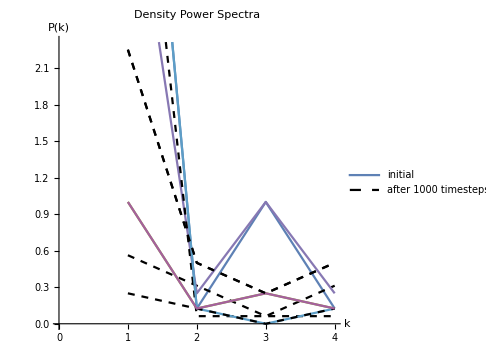

```mathematica
r1PSgraph =  ListLinePlot[{r1FT100[[1]],r1FT200[[1]],r1FT300[[1]],r1FT400[[1]],r1FT500[[1]],r1FT600[[1]],r1FT700[[1]],r1FT800[[1]],r1FT900[[1]],r1FT1000[[1]]},PlotStyle->{Automatic, {Black, Dashed}},
PlotRange->Automatic,AspectRatio->1,ImageSize->Medium,PlotLegends->{"initial","after 1000 timesteps"},AxesLabel->{"k","P(k)"}, PlotLabel-> "Density Power Spectra"]
```

```mathematica
bp1PSgraph =  ListLinePlot[{bp1FT100[[1]],bp1FT200[[1]],bp1FT300[[1]],bp1FT400[[1]],bp1FT500[[1]],bp1FT600[[1]],bp1FT700[[1]],bp1FT800[[1]],bp1FT900[[1]],bp1FT1000[[1]]},PlotStyle->{Automatic, {Black, Dashed}},
PlotRange->Automatic,AspectRatio->1,ImageSize->Medium,PlotLegends->{"initial","after 1000 timesteps"},AxesLabel->{"k","P(k)"}, PlotLabel-> "Density Power Spectra"]
```

-Graphics-

```mathematica
comp1PSgraph = ListLinePlot[{r1FT1000[[1]],bp1FT1000[[1]]},PlotStyle->{Automatic, {Black, Dashed}},
PlotRange->Automatic,AspectRatio->1,ImageSize->Medium,PlotLegends->{"initial","after 1000 timesteps"},AxesLabel->{"k","P(k)"}, PlotLabel-> "Density Power Spectra"]
```

ListLinePlot::lpn: {{{1.,2.25},{2.,0.5},{3.,0.25},{4.,0.5}},{}} is not a list of numbers or pairs of numbers.

ListLinePlot[{{2.25,0.5,0.25,0.5},Abs[Fourier[{{}}]]},PlotStyle→{Automatic,{GrayLevel[0],Dashing[{Small,Small}]}},PlotRange→Automatic,AspectRatio→1,ImageSize→Medium,PlotLegends→{initial,after 1000 timesteps},AxesLabel→{k,P(k)},PlotLabel→Density Power Spectra]

### version 2

#### NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) leapfrog with dimensionless units 100 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp2pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",1;;100,6;;7}];
bp2pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",100;;200,6;;7}];
bp2pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",1000;;1100,6;;7}];
bp2pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",2000;;2100,6;;7}];
bp2pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",3000;;3100,6;;7}];
bp2pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",10000;;10100,6;;7}];
bp2pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",20000;;20100,6;;7}];
bp2pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",30000;;30100,6;;7}];
bp2pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",40000;;40100,6;;7}];
bp2pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",50000;;50100,6;;7}];
bp2pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",60000;;60100,6;;7}];
bp2pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",70000;;70100,6;;7}];
bp2pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",80000;;80100,6;;7}];
bp2pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",90000;;90100,6;;7}];
bp2pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",100000;;100100,6;;7}];

r2pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",1;;100,6;;7}];
r2pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",100;;200,6;;7}];
r2pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",1000;;1100,6;;7}];
r2pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",2000;;2100,6;;7}];
r2pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",3000;;3100,6;;7}];
r2pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",10000;;10100,6;;7}];
r2pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",20000;;20100,6;;7}];
r2pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",30000;;30100,6;;7}];
r2pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",40000;;40100,6;;7}];
r2pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",50000;;50100,6;;7}];
r2pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",60000;;60100,6;;7}];
r2pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",70000;;70100,6;;7}];
r2pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",80000;;80100,6;;7}];
r2pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",90000;;90100,6;;7}];
r2pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",100000;;100100,6;;7}];

bp2vel1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",1;;100,9;;10}];
bp2vel2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",100;;200,9;;10}];
bp2vel10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",1000;;1100,9;;10}];
bp2vel20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",2000;;2100,9;;10}];
bp2vel30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",3000;;3100,9;;10}];
bp2vel100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",10000;;10100,9;;10}];
bp2vel200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",20000;;20100,9;;10}];
bp2vel300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",30000;;30100,9;;10}];
bp2vel400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",40000;;40100,9;;10}];
bp2vel500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",50000;;50100,9;;10}];
bp2vel600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",60000;;60100,9;;10}];
bp2vel700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",70000;;70100,9;;10}];
bp2vel800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",80000;;80100,9;;10}];
bp2vel900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",90000;;90100,9;;10}];
bp2vel1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bp2.csv",{"Data",100000;;100100,9;;10}];
(*velocity of particle 1 at each timestep*)
bp2velp1 = {bp2vel1[[1]],bp2vel100[[1]],bp2vel200[[1]],bp2vel300[[1]],bp2vel400[[1]],bp2vel500[[1]],bp2vel600[[1]],bp2vel700[[1]],bp2vel800[[1]],bp2vel900[[1]],bp2vel1000[[1]]};
(*velocity of particle 100 at each timestep*)
bp2velp10 = {bp2vel1[[100]],bp2vel100[[100]],bp2vel200[[100]],bp2vel300[[100]],bp2vel400[[100]],bp2vel500[[100]],bp2vel600[[100]],bp2vel700[[100]],bp2vel800[[100]],bp2vel900[[100]],bp2vel1000[[100]]};


r2vel1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",1;;100,9;;10}];
r2vel2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",100;;200,9;;10}];
r2vel10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",1000;;1100,9;;10}];
r2vel20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",2000;;2100,9;;10}];
r2vel30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",3000;;3100,9;;10}];
r2vel100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",10000;;10100,9;;10}];
r2vel200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",20000;;20100,9;;10}];
r2vel300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",30000;;30100,9;;10}];
r2vel400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",40000;;40100,9;;10}];
r2vel500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",50000;;50100,9;;10}];
r2vel600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",60000;;60100,9;;10}];
r2vel700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",70000;;70100,9;;10}];
r2vel800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",80000;;80100,9;;10}];
r2vel900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",90000;;90100,9;;10}];
r2vel1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/test2.csv",{"Data",100000;;100100,9;;10}];
(*velocity of particle 1 at each timestep*)
r2velp1 = {r2vel1[[1]],r2vel100[[1]],r2vel200[[1]],r2vel300[[1]],r2vel400[[1]],r2vel500[[1]],r2vel600[[1]],r2vel700[[1]],r2vel800[[1]],r2vel900[[1]],r2vel1000[[1]]}
(*velocity of particle 100 at each timestep*)
r2velp100 = {r2vel1[[100]],r2vel100[[100]],r2vel200[[100]],r2vel300[[100]],r2vel400[[100]],r2vel500[[100]],r2vel600[[100]],r2vel700[[100]],r2vel800[[100]],r2vel900[[100]],r2vel1000[[100]]}
```

{{0.394524,-6.27079},{-5.33952,-3.31181},{-5.61442,2.82067},{-0.530288,6.2608},{5.06009,3.7249},{5.8205,-2.36647},{1.02519,-6.19895},{-4.7487,-4.11447},{-5.98993,1.89739},{-1.51366,6.09811},{4.40735,4.4781}}

{{-1.1542×10^-15,-6.28319},{-5.56696,-2.91333},{-5.39361,3.22286},{-0.0719976,6.28281},{5.31842,3.34572},{5.63229,-2.7849},{0.570096,-6.25723},{-5.03629,-3.75697},{-5.83549,2.32944},{-1.06462,6.19231},{4.72238,4.14453}}

```mathematica
r2AMp1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,1}];
r2AMp2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,2}];
r2AMp3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,3}];
r2AMp4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,4}];
r2AMp5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,5}];
r2AMp6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,6}];
r2AMp7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,7}];
r2AMp8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,8}];
r2AMp9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,9}];
r2AMp10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,10}];
r2AMp20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,20}];
r2AMp30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,30}];
r2AMp40 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,40}];
r2AMp50 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,50}];
r2AMp60 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,60}];
r2AMp70 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,70}];
r2AMp80 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,80}];
r2AMp90 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,90}];
r2AMp100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/AM2.csv",{"Data",1;;1000,100}];

bp2AMp1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,1}];
bp2AMp2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,2}];
bp2AMp3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,3}];
bp2AMp4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,4}];
bp2AMp5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,5}];
bp2AMp6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,6}];
bp2AMp7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,7}];
bp2AMp8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,8}];
bp2AMp9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,9}];
bp2AMp10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,10}];
bp2AMp20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,20}];
bp2AMp30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,30}];
bp2AMp40 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,40}];
bp2AMp50 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,50}];
bp2AMp60 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,60}];
bp2AMp70 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,70}];
bp2AMp80 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,80}];
bp2AMp90 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,90}];
bpAMp100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpAM2.csv",{"Data",1;;1000,100}];


r2SD = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/SD2.csv",{"Data",1;;1000,1;;2}];
bp2SD = Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpSD2.csv",{"Data",1;;1000,1;;2}];
(*updated up to here*)

r2PS1 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS2.csv",{"Data",1,1;;4}];
r2PS100 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS2.csv",{"Data",100,1;;4}];
r2PS200 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS2.csv",{"Data",200,1;;4}];
r2PS300 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS2.csv",{"Data",300,1;;4}];
r2PS400 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS2.csv",{"Data",400,1;;4}];
r2PS500 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS2.csv",{"Data",500,1;;4}];
r2PS600 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS2.csv",{"Data",600,1;;4}];
r2PS700 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS2.csv",{"Data",700,1;;4}];
r2PS800 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS2.csv",{"Data",800,1;;4}];
r2PS900 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS2.csv",{"Data",900,1;;4}];
r2PS1000 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/PS2.csv",{"Data",1000,1;;4}];

bp1PS1 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",1,1;;4}];
bp1PS100 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",100,1;;4}];
bp1PS200 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",200,1;;4}];
bp1PS300 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",300,1;;4}];
bp1PS400 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",400,1;;4}];
bp1PS500 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",500,1;;4}];
bp1PS600 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",600,1;;4}];
bp1PS700 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",700,1;;4}];
bp1PS800 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",800,1;;4}];
bp1PS900 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",900,1;;4}];
bp1PS1000 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/mathematica/bpPS1.csv",{"Data",1000,1;;4}];

r1FT1 = Abs[Fourier[{r1PS1}]]^2;
r1FT100 = Abs[Fourier[{r1PS100}]]^2;
r1FT200 = Abs[Fourier[{r1PS200}]]^2;
r1FT300 = Abs[Fourier[{r1PS300}]]^2;
r1FT400 = Abs[Fourier[{r1PS400}]]^2;
r1FT500 = Abs[Fourier[{r1PS500}]]^2;
r1FT600 = Abs[Fourier[{r1PS600}]]^2;
r1FT700 = Abs[Fourier[{r1PS700}]]^2;
r1FT800 = Abs[Fourier[{r1PS800}]]^2;
r1FT900 = Abs[Fourier[{r1PS900}]]^2;
r1FT1000 = Abs[Fourier[{r1PS1000}]]^2;

bp1FT1 = Abs[Fourier[{bp1PS1}]]^2;
bp1FT100 = Abs[Fourier[{bp1PS100}]]^2;
bp1FT200 = Abs[Fourier[{bp1PS200}]]^2;
bp1FT300 = Abs[Fourier[{bp1PS300}]]^2; 
bp1FT400 = Abs[Fourier[{bp1PS400}]]^2;(*start differing here*)
bp1FT500 = Abs[Fourier[{bp1PS500}]]^2;
bp1FT600 = Abs[Fourier[{bp1PS600}]]^2;
bp1FT700 = Abs[Fourier[{bp1PS700}]]^2;
bp1FT800 = Abs[Fourier[{bp1PS800}]]^2;
bp1FT900 = Abs[Fourier[{bp1PS900}]]^2;
bp1FT1000 = Abs[Fourier[{bp1PS1000}]]^2;
```

Fourier::fftl: Argument {{}} is not a non-empty list or rectangular array of numeric quantities.